# Diagnostic Performance vs Latent Dimension

## Parameters regression

This notebook summarizes diagonal-test performance for ENCA models trained with different latent-space dimensions. For each z dimension, the diagnostic output provides the Pearson correlation and normalized RMSE for each physical parameter. The plots compare correlation with a baseline-corrected performance score, using the prior-mean predictor as the zero-performance reference.

The numerical pairs below are copied from the output of diag_test.py. For each parameter and latent dimension, the first number is the Pearson correlation between true and predicted parameter values, and the second number is RMSE divided by the prior range, reported in percent.

### Performance scores

```mathematica
τ5={0.9353,10.8};
T5={0.9510,9.3};
Nd5={0.9121,13.1};
σ5={0.9146,11.8};
Bmax5={0.9733,7.8};
```

```mathematica
τ5cpu={0.9302,10.6};
T5cpu={0.9334,10.7};
Nd5cpu={0.3801,27.0};
σ5cpu={0.8997,12.8};
Bmax5cpu={0.9088,12.3};
```

```mathematica
τ6={0.9776,6.1};
T6={0.8528,15.4};
Nd6={0.4464,26.0};
σ6={0.0035,29.3};
Bmax6={0.9367,10.0};
```

```mathematica
τ6cpu={0.9799,5.7};
T6cpu={0.8537,15.4};
Nd6cpu={0.4677,25.5};
σ6cpu={0.0035,29.3};
Bmax6cpu={0.9505,8.9};
```

```mathematica
τ7={0.9832,5.4};
T7={0.9827,5.5};
Nd7={0.9479,9.3};
σ7={-0.0468,29.5};
Bmax7={0.9804,5.9};
```

```mathematica
τ7cpu={0.9816,5.5};
T7cpu={0.9780,6.2};
Nd7cpu={0.9611,7.9};
σ7cpu={0.9098,12.1};
Bmax7cpu={0.9822,5.7};
```

```mathematica
τ7bcpu={0.9789,5.9};
T7bcpu={0.9737,6.7};
Nd7bcpu={0.9189,11.3};
σ7bcpu={-0.0573,29.9};
Bmax7bcpu={0.9768,6.2};
```

```mathematica
τ7ccpu={0.9916,3.8};
T7ccpu={0.9887,4.4};
Nd7ccpu={0.9628,7.9};
σ7ccpu={0.0146,29.3};
Bmax7ccpu={0.9871,4.7};
```

```mathematica
τ8={0.9826,5.4};
T8={0.9657,7.7};
Nd8={0.8992,12.6};
σ8={0.0179,29.2};
Bmax8={0.9666,7.4};
```

```mathematica
τ8cpu={0.9790,5.9};
T8cpu={0.9549,8.8};
Nd8cpu={0.8845,13.5};
σ8cpu={0.0387,29.4};
Bmax8cpu={0.9672,7.4};
```

```mathematica
τ8bcpu={0.9914,3.8};
T8bcpu={0.9862,4.9};
Nd8bcpu={0.9651,7.6};
σ8bcpu={0.0711,29.3};
Bmax8bcpu={0.9876,4.5};
```

```mathematica
τ9={0.9886,4.3};
T9={0.9802,5.9};
Nd9={0.9570,8.8};
σ9={0.4811,25.6};
Bmax9={0.9841,5.2};
```

```mathematica
τ9cpu={0.9911,3.8};
T9cpu={0.9869,4.8};
Nd9cpu={0.9635,7.7};
σ9cpu={-0.0095,29.3};
Bmax9cpu={0.9872,4.6};
```

```mathematica
τ9bcpu={0.9874,4.6};
T9bcpu={0.9900,4.2};
Nd9bcpu={0.9640,7.7};
σ9bcpu={0.0042,29.3};
Bmax9bcpu={0.9918,3.7};
```

```mathematica
τ9ccpu={0.9835,5.2};
T9ccpu={0.9750,6.6};
Nd9ccpu={0.9510,9.0};
σ9ccpu={0.0360,29.4};
Bmax9ccpu={0.9885,4.3};
```

```mathematica
τ10={0.9847,5.0};
T10={0.9861,4.9};
Nd10={0.9393,10.0};
σ10={-0.0034,29.4};
Bmax10={0.9869,4.6};
```

```mathematica
(*Wrong, discard this*)
(*τ10cpu={0.9874,4.6};
T10cpu={0.9805,5.8};
Nd10cpu={0.9644,7.7};
σ10cpu={0.0531,29.2};
Bmax10cpu={0.9900,4.0};*)
```

```mathematica
τ10bcpu={0.9862,4.8};
T10bcpu={0.9776,6.2};
Nd10bcpu={0.9626,7.8};
σ10bcpu={0.0242,29.3};
Bmax10bcpu={0.9801,5.7};
```

```mathematica
τ10ccpu={0.9857,4.8};
T10ccpu={0.9767,6.3};
Nd10ccpu={0.8991,12.7};
σ10ccpu={-0.0143,29.4};
Bmax10ccpu={0.9518,8.8};
```

```mathematica
τ10dcpu={0.9674,7.3};
T10dcpu={0.9667,7.6};
Nd10dcpu={0.8816,13.6};
σ10dcpu={-0.0282,29.4};
Bmax10dcpu={0.9725,6.7};
```

```mathematica
τ11cpu={0.9883,4.4};
T11cpu={0.9873,4.7};
Nd11cpu={0.9535,8.8};
σ11cpu={0.0411,29.2};
Bmax11cpu={0.9876,4.5};
```

```mathematica
τ12={0.9882,4.4};
T12={0.9841,5.4};
Nd12={0.9388,10.2};
σ12={0.0497,29.2};
Bmax12={0.9896,4.6};
```

```mathematica
τ12cpu={0.9914,3.8};
T12cpu={0.9888,4.4};
Nd12cpu={0.9507,9.1};
σ12cpu={0.0275,29.2};
Bmax12cpu={0.9894,4.2};
```

```mathematica
τ12bcpu={0.9898,4.1};
T12bcpu={0.9840,5.3};
Nd12bcpu={0.9513,8.9};
σ12bcpu={0.6036,23.3};
Bmax12bcpu={0.9888,4.3};
```

```mathematica
τ12ccpu={0.9916,3.7};
T12ccpu={0.9901,4.1};
Nd12ccpu={0.9687,7.1};
σ12ccpu={-0.0115,29.4};
Bmax12ccpu={0.9914,3.7};
```

```mathematica
τ13cpu={0.9872,4.6};
T13cpu={0.9862,4.9};
Nd13cpu={0.9346,10.2};
σ13cpu={-0.0296,29.4};
Bmax13cpu={0.9903,4.0};
```

```mathematica
τ14={0.9907,3.9};
T14={0.9896,4.3};
Nd14={0.9638,7.6};
σ14={0.0044,29.3};
Bmax14={0.9910,3.8};
```

```mathematica
τ14b={0.9907,3.9};
T14b={0.9898,4.2};
Nd14b={0.9498,9.0};
σ14b={0.7395,19.7};
Bmax14b={0.9882,4.4};
```

```mathematica
τ14cpu={0.9926,3.5};
T14cpu={0.9924,3.6};
Nd14cpu={0.9644,7.7};
σ14cpu={-0.0433,29.4};
Bmax14cpu={0.9916,3.7};
```

```mathematica
τ14bcpu={0.9942,3.1};
T14bcpu={0.9916,3.8};
Nd14bcpu={0.9663,7.4};
σ14bcpu={-0.0231,29.4};
Bmax14bcpu={0.9927,3.5};
```

```mathematica
τ15cpu={0.9928,3.4};
T15cpu={0.9926,3.6};
Nd15cpu={0.9711,6.8};
σ15cpu={0.0031,29.3};
Bmax15cpu={0.9911,3.8};
```

```mathematica
(* training: 20260521_enca_z16_3*)
τ16={0.9891,4.3};
T16={0.9857,5.0};
Nd16={0.9610,7.9};
σ16={-0.0579,29.5};
Bmax16={0.9848,5.0};
```

```mathematica
(*training 20260527_enca_z16b_3*)
τ16b={0.9926,3.5};
T16b={0.9896,4.2};
Nd16b={0.9662,7.4};
σ16b={-0.0245,29.5};
Bmax16b={0.9933,3.4};
```

```mathematica
τ16cpu={0.9867,4.7};
T16cpu={0.9861,4.9};
Nd16cpu={0.9618,7.9};
σ16cpu={0.0136,29.3};
Bmax16cpu={0.9874,4.6};
```

```mathematica
τ16bcpu={0.9928,3.5};
T16bcpu={0.9831,5.4};
Nd16bcpu={0.9686,7.2};
σ16bcpu={-0.0491,29.5};
Bmax16bcpu={0.9928,3.4};
```

```mathematica
τ16ccpu={0.9894,4.2};
T16ccpu={0.9860,4.9};
Nd16ccpu={0.9407,9.7};
σ16ccpu={0.0223,29.3};
Bmax16ccpu={0.9878,4.5};
```

```mathematica
τ16dcpu={0.9911,3.8};
T16dcpu={0.9847,5.2};
Nd16dcpu={0.9670,7.5};
σ16dcpu={-0.0052,29.4};
Bmax16dcpu={0.9891,4.3};
```

```mathematica
τ18={0.9947,2.9};
T18={0.9872,4.7};
Nd18={0.9663,7.4};
σ18={0.0084,29.3};
Bmax18={0.9901,4.0};
```

```mathematica
τ18b={0.9929,3.4};
T18b={0.9898,4.2};
Nd18b={0.9720,6.8};
σ18b={0.0018,29.3};
Bmax18b={0.9926,3.5};
```

```mathematica
τ18cpu={0.9905,3.9};
T18cpu={0.9871,4.8};
Nd18cpu={0.9657,7.5};
σ18cpu={-0.0289,29.4};
Bmax18cpu={0.9932,3.4};
```

```mathematica
τ18bcpu={0.9874,4.6};
T18bcpu={0.9805,5.8};
Nd18bcpu={0.9644,7.7};
σ18bcpu={0.0531,29.2};
Bmax18bcpu={0.9900,4.0};
```

```mathematica
τ18ccpu={0.9895,4.2};
T18ccpu={0.9848,5.1};
Nd18ccpu={0.9538,8.7};
σ18ccpu={0.0267,29.2};
Bmax18ccpu={0.9909,3.9};
```

```mathematica
τ20={0.9931,3.4};
T20={0.9878,4.6};
Nd20={0.9661,7.4};
σ20={0.0003,29.3};
Bmax20={0.9920,3.6};
```

```mathematica
τ20cpu={0.9950,2.9};
T20cpu={0.9911,3.9};
Nd20cpu={0.9632,7.7};
σ20cpu={0.0014,29.3};
Bmax20cpu={0.9945,3.0};
```

```mathematica
τ20bcpu={0.9917,3.7};
T20bcpu={0.9876,4.6};
Nd20bcpu={0.9619,7.9};
σ20bcpu={-0.0032,29.3};
Bmax20bcpu={0.9900,4.1};
```

```mathematica
zDims={5,6,7,8,9,10,12,14,14,16,16,18,18,20};
zDimsCPU={5,6,7,7,7,8,8,9,9,9,10,10,10,11,12,12,12,13,14,14,15,16,16,16,16,18,18,18,20,20};
```

```mathematica
paramData=<|"τ"->{τ5,τ6,τ7,τ8,τ9,τ10,τ12,τ14,τ14b,τ16,τ16b,τ18,τ18b,τ20},"T"->{T5,T6,T7,T8,T9,T10,T12,T14,T14b,T16,T16b,T18,T18b,T20},"Nd"->{Nd5,Nd6,Nd7,Nd8,Nd9,Nd10,Nd12,Nd14,Nd14b,Nd16,Nd16b,Nd18,Nd18b,Nd20},"σ"->{σ5,σ6,σ7,σ8,σ9,σ10,σ12,σ14,σ14b,σ16,σ16b,σ18,σ18b,σ20},"Bmax"->{Bmax5,Bmax6,Bmax7,Bmax8,Bmax9,Bmax10,Bmax12,Bmax14,Bmax14b,Bmax16,Bmax16b,Bmax18,Bmax18b,Bmax20}|>;
```

```mathematica
paramDataCPU=<|"τ"->{τ5cpu,τ6cpu,τ7cpu,τ7bcpu,τ7ccpu,τ8cpu,τ8bcpu,τ9cpu,τ9bcpu,τ9ccpu,τ10bcpu,τ10ccpu,τ10dcpu,τ11cpu,τ12cpu,τ12bcpu,τ12ccpu,τ13cpu,τ14cpu,τ14bcpu,τ15cpu,τ16cpu,τ16bcpu,τ16ccpu,τ16dcpu,τ18cpu,τ18bcpu,τ18ccpu,τ20cpu,τ20bcpu},"T"->{T5cpu,T6cpu,T7cpu,T7bcpu,T7ccpu,T8cpu,T8bcpu,T9cpu,T9bcpu,T9ccpu,T10bcpu,T10ccpu,T10dcpu,T11cpu,T12cpu,T12bcpu,T12ccpu,T13cpu,T14cpu,T14bcpu,T15cpu,T16cpu,T16bcpu,T16ccpu,T16dcpu,T18cpu,T18bcpu,T18ccpu,T20cpu,T20bcpu},"Nd"->{Nd5cpu,Nd6cpu,Nd7cpu,Nd7bcpu,Nd7ccpu,Nd8cpu,Nd8bcpu,Nd9cpu,Nd9bcpu,Nd9ccpu,Nd10bcpu,Nd10ccpu,Nd10dcpu,Nd11cpu,Nd12cpu,Nd12bcpu,Nd12ccpu,Nd13cpu,Nd14cpu,Nd14bcpu,Nd15cpu,Nd16cpu,Nd16bcpu,Nd16ccpu,Nd16dcpu,Nd18cpu,Nd18bcpu,Nd18ccpu,Nd20cpu,Nd20bcpu},"σ"->{σ5cpu,σ6cpu,σ7cpu,σ7bcpu,σ7ccpu,σ8cpu,σ8bcpu,σ9cpu,σ9bcpu,σ9ccpu,σ10bcpu,σ10ccpu,σ10dcpu,σ11cpu,σ12cpu,σ12bcpu,σ12ccpu,σ13cpu,σ14cpu,σ14bcpu,σ15cpu,σ16cpu,σ16bcpu,σ16ccpu,σ16dcpu,σ18cpu,σ18bcpu,σ18ccpu,σ20cpu,σ20bcpu},"Bmax"->{Bmax5cpu,Bmax6cpu,Bmax7cpu,Bmax7bcpu,Bmax7ccpu,Bmax8cpu,Bmax8bcpu,Bmax9cpu,Bmax9bcpu,Bmax9ccpu,Bmax10bcpu,Bmax10ccpu,Bmax10dcpu,Bmax11cpu,Bmax12cpu,Bmax12bcpu,Bmax12ccpu,Bmax13cpu,Bmax14cpu,Bmax14bcpu,Bmax15cpu,Bmax16cpu,Bmax16bcpu,Bmax16ccpu,Bmax16dcpu,Bmax18cpu,Bmax18bcpu,Bmax18ccpu,Bmax20cpu,Bmax20bcpu}|>;
```

### Plots

```mathematica
corr[param_]:=paramData[param][[All,1]];

baselineError=1/Sqrt[12];
perf[param_]:=1-(paramData[param][[All,2]]/100)/baselineError;
```

Performance score 
For each physical parameter, the diagnostic test reports 
normalized RMSE=RMSE/prior range.
Since the parameters are sampled uniformly from their prior intervals, a trivial baseline predictor is one that always predicts the prior mean, i.e. the midpoint of the allowed interval.
For a uniform distribution on[a,b], the standard deviation is (b-a)/Sqrt[12].
Therefore,the normalized RMSE of this trivial mean predictor is 
baselineError=((b-a)/Sqrt[12])/(b-a)=1/Sqrt[12].
We define the baseline-corrected performance score as 
performance=1-normalizedRMSE/baselineError=1-(RMSE/prior range)/(1/Sqrt[12]).

Interpretation:
performance=1  --- perfect prediction,RMSE=0 
performance=0  --- no better than always predicting the prior mean 
performance<0 ---  worse than the prior-mean predictor 

Thus this score measures the fraction of the naive baseline error removed by the encoder.
For example, performance=0.6 means that the model has reduced the RMSE by about 60% relative to always predicting the prior mean.

```mathematica
dualAxisPlot[title_,corrVals_,perfVals_]:=Module[{perfData,corrData,gridZDims},
perfData=Transpose[{zDims,perfVals}];
corrData=Transpose[{zDims,corrVals}];
gridZDims=Range[Min[zDims],Max[zDims]];
ListLinePlot[{perfData,corrData},
Frame->True,Axes->False,
PlotMarkers->{Automatic,16},
PlotStyle->{Blue,Darker[Red]},PlotLegends->Placed[{"1 - (mean) normalized RMSE","mean corr"},Above],FrameLabel->{"latent dimension z","performance score",None,"correlation"},FrameTicks->{{Automatic,Automatic},{Thread[{zDims,zDims}],None}},PlotRange->{{Min[zDims]-1,Max[zDims]+1},{-0.05,1.02}},GridLines->{gridZDims,Automatic},
FrameStyle->Directive[Black,AbsoluteThickness[1.6]],
FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,16],
ImageSize->620,
PlotLabel->Style[title,17,Black]]]
```

```mathematica
corrCPU[param_] := paramDataCPU[param][[All, 1]];
perfCPU[param_] := 1 - ((paramDataCPU[param][[All, 2]]/100)/baselineError);

cpuSeriesFor[corrVals_, perfVals_] := Module[{param},
  param = SelectFirst[
    Keys[paramData],
    corr[#] === corrVals && perf[#] === perfVals &,
    None
  ];
  If[param =!= None,
    {corrCPU[param], perfCPU[param]},
    If[
      ValueQ[paramsNoSigma] && corrVals === meanCorrNoSigma &&
        perfVals === meanPerfNoSigma,
      {
        Mean /@ Transpose[corrCPU /@ paramsNoSigma],
        Mean /@ Transpose[perfCPU /@ paramsNoSigma]
      },
      {{}, {}}
    ]
  ]
];

dualAxisPlot[title_, corrVals_, perfVals_] := Module[
  {perfData, corrData, cpuCorrVals, cpuPerfVals, perfDataCPU, corrDataCPU,
   plotData, plotStyles, plotMarkers, plotLegends, allZDims, gridZDims},
  perfData = Transpose[{zDims, perfVals}];
  corrData = Transpose[{zDims, corrVals}];
  {cpuCorrVals, cpuPerfVals} = cpuSeriesFor[corrVals, perfVals];
  perfDataCPU = If[cpuPerfVals === {}, {}, Transpose[{zDimsCPU, cpuPerfVals}]];
  corrDataCPU = If[cpuCorrVals === {}, {}, Transpose[{zDimsCPU, cpuCorrVals}]];
  plotData = DeleteCases[{perfData, corrData, perfDataCPU, corrDataCPU}, {}];
  plotStyles = Take[
    {Blue, Darker[Red], Directive[Blue, Dashed], Directive[Darker[Red], Dashed]},
    Length[plotData]
  ];
  plotMarkers = Take[
    {{"●", 16}, {"■", 16}, {"○", 16},
     {"□", 16}},
    Length[plotData]
  ];
  plotLegends = Take[
    {"1 - (mean) normalized RMSE", "mean corr",
     "CPU 1 - (mean) normalized RMSE", "CPU mean corr"},
    Length[plotData]
  ];
  allZDims = Sort[Union[zDims, If[cpuCorrVals === {}, {}, zDimsCPU]]];
  gridZDims = Range[Min[allZDims], Max[allZDims]];
  ListLinePlot[
    plotData,
    Frame -> True,
    Axes -> False,
    PlotMarkers -> plotMarkers,
    PlotStyle -> plotStyles,
    PlotLegends -> Placed[plotLegends, Above],
    FrameLabel -> {"latent dimension z", "performance score", None,
      "correlation"},
    FrameTicks -> {{Automatic, Automatic}, {Thread[{allZDims, allZDims}], None}},
    PlotRange -> {{Min[allZDims] - 1, Max[allZDims] + 1}, {-0.1, 1.02}},
    GridLines -> {gridZDims, Automatic},
    FrameStyle -> Directive[Black, AbsoluteThickness[1.6]],
    FrameTicksStyle -> Directive[Black, 14],
    LabelStyle -> Directive[Black, 16],
    ImageSize -> 620,
    PlotLabel -> Style[title, 17, Black]
  ]
]
```

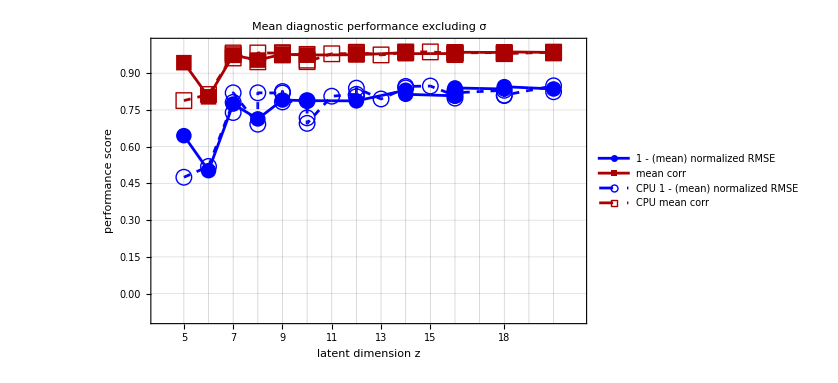

```mathematica
paramsNoSigma={"τ","T","Nd","Bmax"};

meanCorrNoSigma=Mean/@Transpose[corr/@paramsNoSigma];
meanPerfNoSigma=Mean/@Transpose[perf/@paramsNoSigma];

dualAxisPlot["Mean diagnostic performance excluding σ",meanCorrNoSigma,meanPerfNoSigma]
```

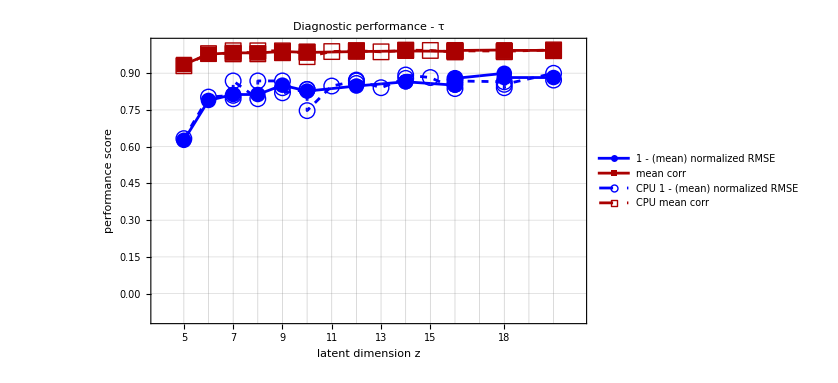

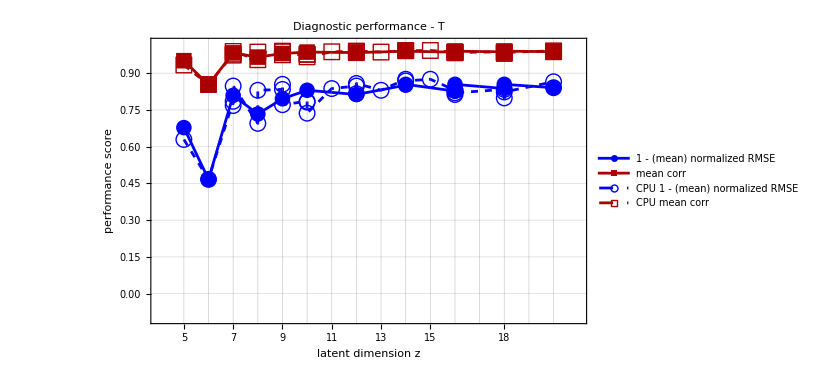

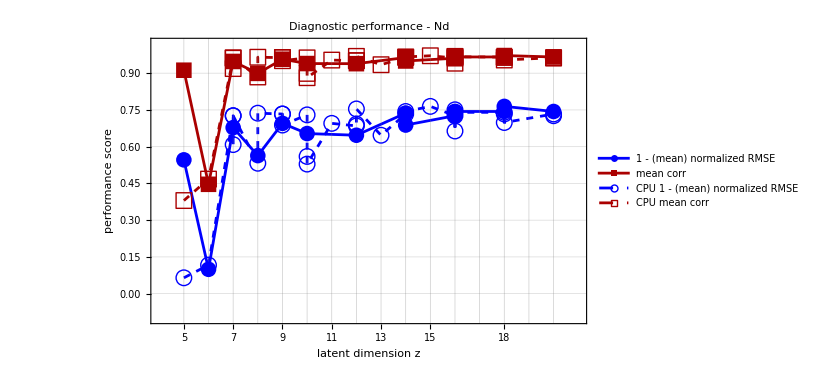

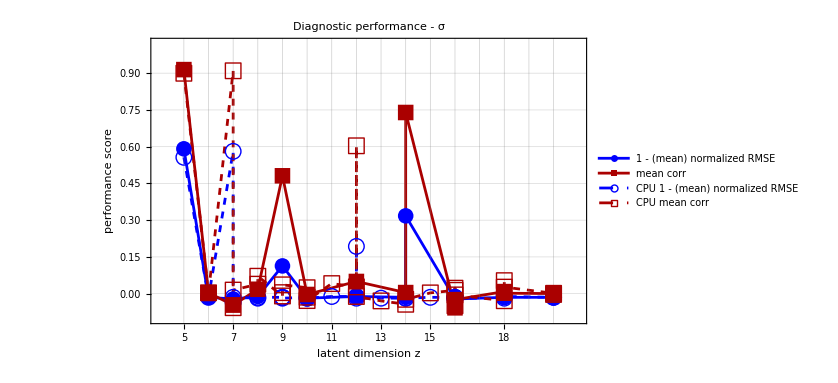

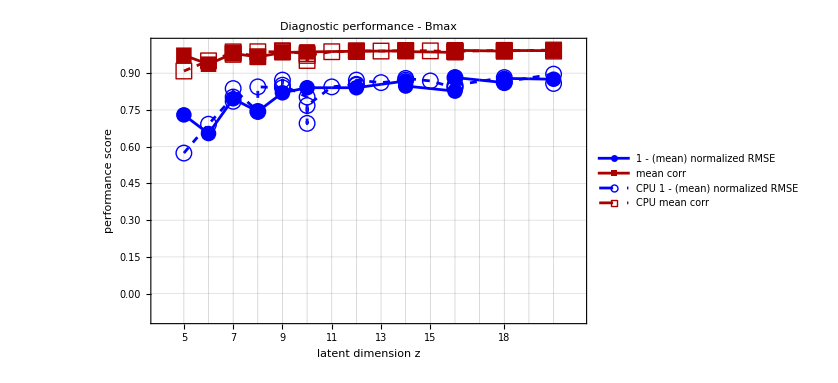

```mathematica
dualAxisPlot["Diagnostic performance - τ",corr["τ"],perf["τ"]]
dualAxisPlot["Diagnostic performance - T",corr["T"],perf["T"]]
dualAxisPlot["Diagnostic performance - Nd",corr["Nd"],perf["Nd"]]
dualAxisPlot["Diagnostic performance - σ",corr["σ"],perf["σ"]]
dualAxisPlot["Diagnostic performance - Bmax",corr["Bmax"],perf["Bmax"]]
```

## Reconstruction

Parameters : tau = 5, T = 6, Nd = 12, sigma = 0.02, Bmax = 8
nseeds = 10

Reconstruction performance
The reconstruction tests are run with the same physical parameters and the same number of noise realizations for each latent dimension, so the reported mean_RMSE values from recon_test.py are directly comparable. Lower mean_RMSE means better reconstruction.

To plot a higher-is-better score, the RMSE values are normalized by the worst RMSE among the currently tested latent dimensions:

reconstruction performance = 1 - meanRMSE/rmseRef,

where rmseRef = Max[Join[meanRMSE, meanRMSEcpu]]. With this definition, performance = 1 would correspond to perfect reconstruction, while performance = 0 corresponds to the worst model in the current comparison set. For example, a value of 0.47 means that the model reduces the reconstruction RMSE by about 47% relative to the current worst model.

```mathematica
zdim={5,6,7,8,9,10,12,14,14,16,16,18,18,20};
meanRMSE={111.62,84.7185,46.3609,45.0629,67.978,51.158,48.7618,57.3424,61.695,66.584,47.538,34.693,42.4852,53.1832};
```

```mathematica
zdimCPU={5,6,7,7,7,8,8,9,9,9,10,10,10,11,12,12,12,13,14,14,15,16,16,16,16,18,18,18,20,20};
meanRMSEcpu={107.729,46.1961,126.544,46.0253,96.4939,45.8176,30.8796,41.5265,32.3264,60.9754,42.3789,50.3177,79.4767,49.8666,40.5563,55.0343,37.9044,53.6159,35.1991,42.3242,36.1268,33.6647,36.0377,65.3836,48.6246,39.7918,31.7558,46.021,26.2812,65.2819};
```

```mathematica
rmseRef=Max[Join[meanRMSE,meanRMSEcpu]];
reconPerf=1-meanRMSE/rmseRef;
reconPerfCPU=1-meanRMSEcpu/rmseRef;
```

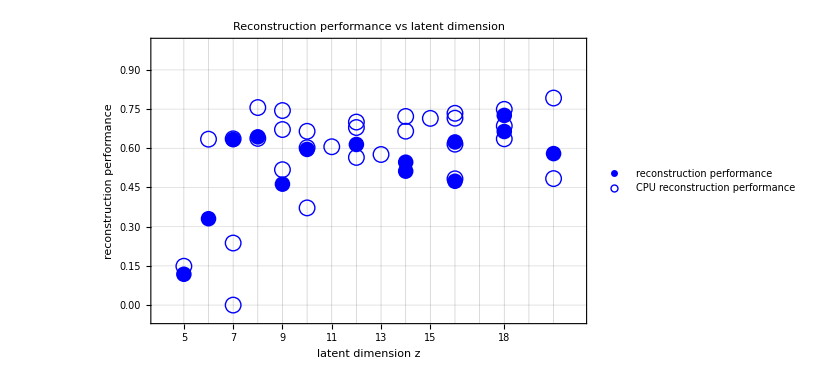

```mathematica
reconZDimsAll = Sort[Union[zdim, zdimCPU]];

reconGridZDims = Range[Min[reconZDimsAll], Max[reconZDimsAll]];
ListPlot[
  {
    Transpose[{zdim, reconPerf}],
    Transpose[{zdimCPU, reconPerfCPU}]
  },
  Frame -> True,
  Axes -> False,
  PlotMarkers -> {{"●", 16}, {"○", 16}},
  PlotStyle -> {Blue, Directive[Blue, Dashed]},
  PlotLegends -> Placed[{"reconstruction performance",
    "CPU reconstruction performance"}, Above],
  FrameLabel -> {"latent dimension z", "reconstruction performance"},
  PlotLabel -> Style["Reconstruction performance vs latent dimension", 17, Black],
  FrameTicks -> {{Automatic, Automatic}, {Thread[{reconZDimsAll, reconZDimsAll}],
    None}},
  GridLines -> {reconGridZDims, Automatic},
  PlotRange -> {{Min[reconZDimsAll] - 1, Max[reconZDimsAll] + 1}, {-0.05, 1}},
  FrameStyle -> Directive[Black, AbsoluteThickness[1.6]],
  FrameTicksStyle -> Directive[Black, 14],
  LabelStyle -> Directive[Black, 16],
  ImageSize -> 620
]
```

Pooled reconstruction performance with run-to-run variability
We found no reason to treat CPU and GPU runs separately, and interpret their differences as part of training stochasticity. CPU and GPU trainings are treated as independent realizations of the same stochastic training procedure. Hardware-dependent numerical differences may change the optimization trajectory, but are not assumed to introduce a systematic performance bias; instead, they are included in the observed run-to-run variability.

For each latent dimension z, all available CPU and GPU runs are pooled. The plotted mean is the arithmetic mean of the reconstruction performance values at that z. The vertical error bar is the sample standard deviation across the available runs at that z. Latent dimensions with only one available run are not included in the pooled mean/error-bar layer, but their individual run is still shown as a faint point. Faint filled circles show the individual GPU runs, and faint open circles show the individual CPU runs.

Pooled mean with run-to-run variability:

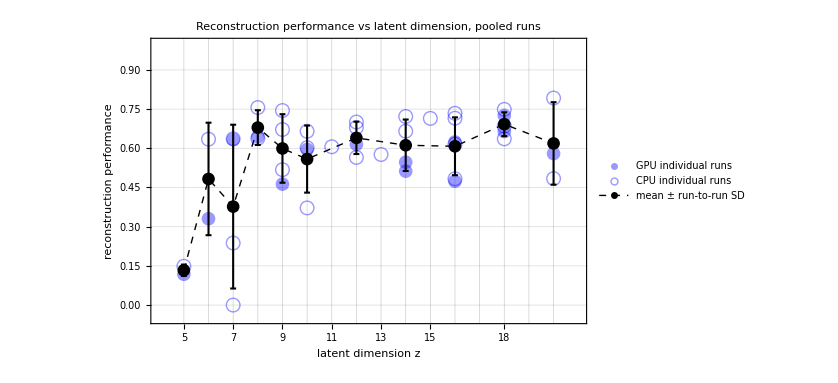

```mathematica
reconRunPairs = Join[
   Transpose[{zdim, reconPerf}],
   Transpose[{zdimCPU, reconPerfCPU}]
   ];

reconGroupedPairs = Select[GatherBy[SortBy[reconRunPairs, First], First], Length[#] > 1 &];

reconMeanSD = ({#[[1, 1]], Mean[#[[All, 2]]],
      If[Length[#] > 1, StandardDeviation[#[[All, 2]]], 0]} & /@ reconGroupedPairs);

reconMeanPts = reconMeanSD[[All, {1, 2}]];

reconErrorBars = Flatten[
   ({Line[{{#[[1]], #[[2]] - #[[3]]}, {#[[1]], #[[2]] + #[[3]]}}],
       Line[{{#[[1]] - 0.12, #[[2]] - #[[3]]}, {#[[1]] + 0.12, #[[2]] - #[[3]]}}],
       Line[{{#[[1]] - 0.12, #[[2]] + #[[3]]}, {#[[1]] + 0.12, #[[2]] + #[[3]]}}]} & /@ reconMeanSD),
   1
   ];

ListPlot[
  {Transpose[{zdim, reconPerf}], Transpose[{zdimCPU, reconPerfCPU}], reconMeanPts},
  Joined -> {False, False, True},
  Frame -> True,
  Axes -> False,
  PlotMarkers -> {{"●", 14}, {"○", 14}, {"●", 13}},
  PlotStyle -> {
    Directive[Blue, Opacity[0.4]],
    Directive[Blue, Opacity[0.4], Dashed],
    Directive[Black, Dashed, AbsoluteThickness[1]]
    },
  Epilog -> {Black, AbsoluteThickness[1.5], reconErrorBars},
  PlotLegends -> Placed[
    {"GPU individual runs", "CPU individual runs", "mean ± run-to-run SD"},
    Above
    ],
  FrameLabel -> {"latent dimension z", "reconstruction performance"},
  PlotLabel -> Style["Reconstruction performance vs latent dimension, pooled runs", 17, Black],
  FrameTicks -> {{Automatic, Automatic}, {Thread[{reconZDimsAll, reconZDimsAll}], None}},
  GridLines -> {reconGridZDims, Automatic},
  PlotRange -> {{Min[reconZDimsAll] - 1, Max[reconZDimsAll] + 1}, {-0.05, 1}},
  FrameStyle -> Directive[Black, AbsoluteThickness[1.6]],
  FrameTicksStyle -> Directive[Black, 14],
  LabelStyle -> Directive[Black, 16],
  ImageSize -> 620
  ]
```